# Check Root Finders nx(nz)

## Open Additional files:

## Get dispersion routines by evaluating Disper_no_package.nb Get plotting and printing routines by evaluating PlotPack.nb

## Data

```mathematica
dataSet="DIII-D ECH";
```

### RF Parameters

```mathematica
freq=55990;
c=3. 10^8;
k0=(2 N[π] freq 10^6)/c;
kz= 20;
nz  =kz/k0;
nz=0.1;
```

### Plasma Parameters

```mathematica
ne0=0.3×10^20;
B0=1.8;
etaList=Table[0.,{i,1,5}];
etaList⟦1⟧=0.;etaList⟦2⟧=0.;etaList⟦3⟧=0.0;
etaList⟦4⟧=0.;etaList⟦5⟧=0.;

TList=Table[0.,{i,1,6}];
TList⟦1⟧=1.0;TList⟦2⟧=0.;
TList⟦3⟧=0.0 ;TList⟦4⟧=0.;
TList⟦5⟧=0.;TList⟦6⟧=0.;

modelList =Table[0,{i,1,6}];
modelList[[1]]=1; modelList[[2]]=1;
modelList[[3]]=0; modelList[[4]]=0;
modelList[[5]]=0; modelList[[6]]=0;

nminList=Table[0.,{i,1,6}];
nminList⟦1⟧=-2;nminList⟦2⟧=-2;
nminList⟦3⟧=-2;nminList⟦4⟧=-2;
nminList⟦5⟧=-2;nminList⟦6⟧=-2;

nmaxList=Table[0.,{i,1,6}];
nmaxList⟦1⟧=2;nmaxList⟦2⟧=2;
nmaxList⟦3⟧=2;nmaxList⟦4⟧=2;
nmaxList⟦5⟧=2;nmaxList⟦6⟧=2;
```

## Find Roots

### Cold Plasma

```mathematica
rootsCold=nxColdDisFS[freq,ne0,B0,nz,etaList]
paramPrint[{dataSet,ne0,B0,freq,nz,etaList}];
```

{0.475614,1.13856}

dataSet=DIII-D ECH

ne0=3.×10^19

B0=1.8

freq=55990

nz=0.1

etaList={0.,0.,0.,0.,0.}

### Warm Plasma (6th order system solved with NSolve)

```mathematica
rootsWarm=WarmDis6[freq,ne0,B0,nz,etaList,TList]
paramPrint[{dataSet,ne0,B0,freq,nz,etaList,TList}];
```

{0.473669,1.13586,16.9318,-0.473669,-1.13586,-16.9318}

dataSet=DIII-D ECH

ne0=3.×10^19

B0=1.8

freq=55990

nz=0.1

etaList={0.,0.,0.,0.,0.}

TList={1.,0.,0.,0.,0.,0.}

### Warm Plasma (6th order system solved with FindRoot i.e. all species modelList=1)

```mathematica
rootsWarm=WarmDis6[freq,ne0,B0,nz,etaList,TList]
model1=Table[1,{i,1,6}];
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model1],{nx,rootsWarm[[1]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model1],{nx,rootsWarm[[2]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model1],{nx,rootsWarm[[3]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model1],{nx,rootsWarm[[4]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model1],{nx,rootsWarm[[5]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model1],{nx,rootsWarm[[6]]}, MaxIterations->30]
paramPrint[{dataSet,ne0,B0,freq,nz,etaList,TList,modelList}];
```

{0.473669,1.13586,16.9318,-0.473669,-1.13586,-16.9318}

{nx→0.473669}

{nx→1.13586}

{nx→16.9318}

{nx→-0.473669}

{nx→-1.13586}

{nx→-16.9318}

dataSet=DIII-D ECH

ne0=3.×10^19

B0=1.8

freq=55990

nz=0.1

etaList={0.,0.,0.,0.,0.}

TList={1.,0.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

### Hot Plasma (Full Maxwellian system solved with FindRoot i.e. all species modelList=2)

```mathematica
rootsWarm=WarmDis6[freq,ne0,B0,nz,etaList,TList]
model2=Table[2,{i,1,6}];
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model2],{nx,rootsWarm[[1]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model2],{nx,rootsWarm[[2]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model2],{nx,rootsWarm[[3]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model2],{nx,rootsWarm[[4]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model2],{nx,rootsWarm[[5]]}, MaxIterations->30]
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model2],{nx,rootsWarm[[6]]}, MaxIterations->30]
paramPrint[{dataSet,ne0,B0,freq,nz,etaList,TList,modelList}];
```

{0.473669,1.13586,16.9318,-0.473669,-1.13586,-16.9318}

{nx→0.47367+0. ⅈ}

{nx→1.13584+0. ⅈ}

{nx→1.13584+0. ⅈ}

{nx→-0.47367+0. ⅈ}

{nx→-1.13584+0. ⅈ}

{nx→-1.13584+0. ⅈ}

dataSet=DIII-D ECH

ne0=3.×10^19

B0=1.8

freq=55990

nz=0.1

etaList={0.,0.,0.,0.,0.}

TList={1.,0.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

modelList={1,1,1,0,0,0}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,1,0,0,0}

### Look at k_⌊ρ. In this case Γ=1/2 (k⊥ρ)^2

```mathematica
Do[
If[TList[[iSpec]]>0.,Print["  species = ",iSpec,"  root = ",iRoot, "  nx = " , rootsWarm[[iRoot]],"  Γ= ", Chop[Warmgamma[freq,B0,rootsWarm[[iRoot]],TList]][[iSpec]]]],{iSpec,1,6},{iRoot,1,6}]
```

species = 1  root = 1  nx = 0.473669  Γ= 0.000542151

species = 1  root = 2  nx = 1.13586  Γ= 0.00311758

species = 1  root = 3  nx = 16.9318  Γ= 0.692751

species = 1  root = 4  nx = -0.473669  Γ= 0.000542151

species = 1  root = 5  nx = -1.13586  Γ= 0.00311758

species = 1  root = 6  nx = -16.9318  Γ= 0.692751

### Print ε for different models

```mathematica
rootsWarm=WarmDis6[freq,ne0,B0,nz,etaList,TList]
nx0 = rootsWarm[[2]];
model=Table[0,{i,1,6}];e0=EpsGeneral[freq,ne0,B0,nz,nx0,etaList,TList,nminList,nmaxList,model,True];
model=Table[1,{i,1,6}];
e1=EpsGeneral[freq,ne0,B0,nz,nx0,etaList,TList,nminList,nmaxList,model,True];
model=Table[2,{i,1,6}];
e2=EpsGeneral[freq,ne0,B0,nz,nx0,etaList,TList,nminList,nmaxList,model,True];
paramPrint[{dataSet,ne0,B0,freq,nz,nx0,etaList,TList,nminList,nmaxList,modelList}];
```

{0.473669,1.13586,16.9318,-0.473669,-1.13586,-16.9318}

EpsGeneral    species=1    model for this species =0

Eps[i]={-4.05748,-4.05748,-0.771485,0.+3.65142 ⅈ,0,0}

EpsGeneral    species=1    model for this species =1

Eps[i]={-4.05131,-4.03077,-0.781845,0.+3.63425 ⅈ,-0.00954312,0.-0.00940534 ⅈ}

EpsGeneral    species=1    model for this species =2

Eps[i]={-4.05134,-4.03094,-0.78181,0.+3.63432 ⅈ,-0.00951364,0.-0.00934682 ⅈ}

dataSet=DIII-D ECH

ne0=3.×10^19

B0=1.8

freq=55990

nz=0.1

nx0=1.13586

etaList={0.,0.,0.,0.,0.}

TList={1.,0.,0.,0.,0.,0.}

nminList={-2,-2,-2,-2,-2,-2}

nmaxList={2,2,2,2,2,2}

modelList={1,1,0,0,0,0}

#### Compare to all Maxwellian

```mathematica
WarmEpsMaxwell[freq,ne0,B0,nz,nx0,etaList,TList,nminList,nmaxList,True]
```

WarmEpsMaxwell    species=1

Eps[i]={-4.05134,-4.03094,-0.78181,0.+3.63432 ⅈ,-0.00951364,0.-0.00934682 ⅈ}

{-3.05134,-3.03094,0.21819,0.+3.63432 ⅈ,-0.00951364,0.-0.00934682 ⅈ}

#### Look at dispersion function values

```mathematica
model=Table[2,{i,1,6}];
DisFuncGeneral[freq,ne0,B0,nz,39.47282432290283,etaList,TList,nminList,nmaxList,model]
```

2.17508+0. ⅈ

```mathematica
FullDisFunc[freq,ne0,B0,nz,30,etaList,TList,nminList,nmaxList]
```

0.346213+0. ⅈ

```mathematica
FullDisFunc[freq,ne0,B0,nz,50.,etaList,TList,nminList,nmaxList]
```

6.87549+0. ⅈ

#### Plot dispersion function values

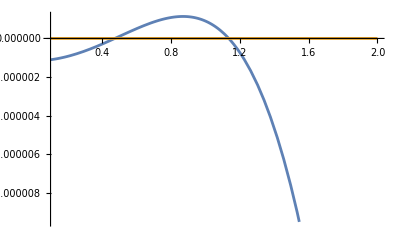

```mathematica
Plot[{Re[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model]],Im[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model]]},{nx,0.1,2}]
```

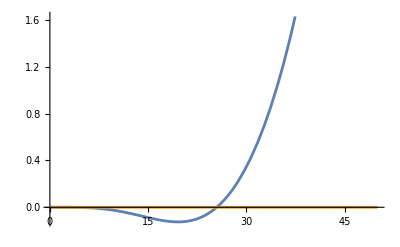

```mathematica
Plot[{Re[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model]],Im[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model]]},{nx,0.1,50}]
```

#### Root find near upper zero in plot

```mathematica
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model],{nx,24, 28}, MaxIterations->30]
```

{nx→25.4606}

```mathematica
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model],{nx,25.4606}, MaxIterations->30]
```

{nx→25.4606+0. ⅈ}

#### Is DisFunc and even function of nx? Plot for negative nx

```mathematica
Plot[{Re[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model]],Im[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model]]},{nx,0.1,2}]
```

-Graphics-

```mathematica
Plot[{Re[DisFuncGeneral[freq,ne0,B0,nz,-nx,etaList,TList,nminList,nmaxList,model]],Im[DisFuncGeneral[freq,ne0,B0,nz,-nx,etaList,TList,nminList,nmaxList,model]]},{nx,0.1,2}]
```

-Graphics-

#### Yes, even function . What if there is and imaginary part?

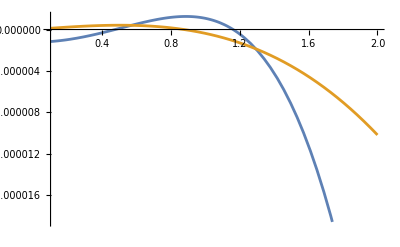

```mathematica
Plot[{Re[DisFuncGeneral[freq,ne0,B0,nz,nx+.1ⅈ,etaList,TList,nminList,nmaxList,model]],Im[DisFuncGeneral[freq,ne0,B0,nz,nx+.1ⅈ,etaList,TList,nminList,nmaxList,model]]},{nx,0.1,2}]
```

```mathematica
Plot[{Re[DisFuncGeneral[freq,ne0,B0,nz,-nx-.1ⅈ,etaList,TList,nminList,nmaxList,model]],Im[DisFuncGeneral[freq,ne0,B0,nz,-nx-.1ⅈ,etaList,TList,nminList,nmaxList,model]]},{nx,0.1,2}]
```

-Graphics-

#### Yes, still even function . What about roots?

```mathematica
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model],{nx,25.4606}, MaxIterations->30]
```

{nx→25.4606+0. ⅈ}

```mathematica
FindRoot[DisFuncGeneral[freq,ne0,B0,nz,nx,etaList,TList,nminList,nmaxList,model],{nx,-25.4606}, MaxIterations->30]
```

{nx→-25.4606+0. ⅈ}